```mathematica
$Assumptions={n>0,p>0,α>0,ω≥0};
```

```mathematica
tri [x_]:=UnitTriangle[x];
boxcar[x_]:=UnitStep[x]-UnitStep[x-1];
gaussian[x_]:=(1/(2Pi))^(1/2)*Exp[-x^2/2];
erf[x_]:=∫_(-∞)^x gaussian[y]ⅆy;
step[x_]:=UnitStep[x];
estep[x_]:=Exp[-x]step[x];
```

```mathematica
nerf[x_]:=NIntegrate[gaussian[y],{y,-∞,x}];
dirichlet[x_,n_]:=Sin[(n+.5)x]/Sin[.5x]
poisson[theta_, r_]:=(1-r^2)/(1-2r*Cos[theta]+r^2)
```

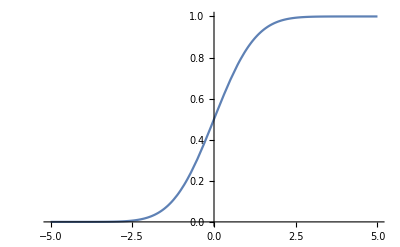

```mathematica
Plot[nerf[x],{x,-5,5}]
```

### 5(1)

(a)

```mathematica
FullSimplify[(Integrate[(n^α*boxcar[x/n])^p,{x,0,n}])^(1/p)]
```

n^(1/p+α)

```mathematica
FullSimplify[(Integrate[(Convolve[n^α*boxcar[x/n],n^α*boxcar[x/n],x,y])^p,{y,-∞,∞}])^(1/p)]
```

2^(1/p) (n^(1+p+2 p α)/(1+p))^(1/p)

```mathematica
l2conv[n_,p_]:=2^(1/p) (n^(1+p+2 p α)/(1+p))^(1/p);
l2box[n_,p_]:=n^(1/p+α);
```

```mathematica
l2conv[n,2]
```

√(2/3) √(n^(3+4 α))

```mathematica
l2box[n,2]*l2box[n,2]
```

n^(1+2 α)

(b)

```mathematica
FullSimplify[(2*Integrate[(n^α*tri[x/n])^p,{x,0,n}])^(1/p)]
```

2^(1/p) n^α (n/(1+p))^(1/p)

(c)

```mathematica
FullSimplify[(Integrate[(n^α*gaussian[x/n])^p,{x,-∞,∞}])^(1/p)]
```

((n^(1+p α) (2 π)^(1/2-p/2))/(√p))^(1/p)

```mathematica
FullSimplify[(2 π)^(1/2/p)]
```

(2 π)^(1/2/p)

```mathematica
(1/(2Pi))^.5
```

0.398942

### 6(1)

(a)

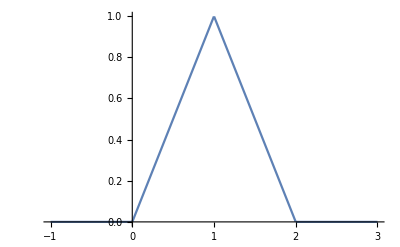

```mathematica
Plot[Convolve[boxcar[x],boxcar[x],x,y],{y,-1,3},PlotRange->Full]
```

(b)

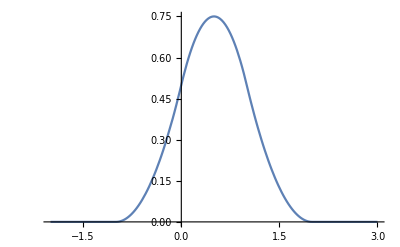

```mathematica
Plot[Convolve[boxcar[x],tri[x],x,y],{y,-2,3},PerformanceGoal->"Speed"]
```

(c)

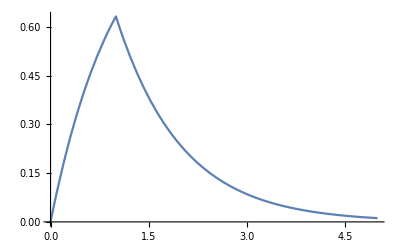

```mathematica
Plot[Convolve[boxcar[x],estep[x],x,y],{y,0,5},PlotRange->Full]
```

(d)

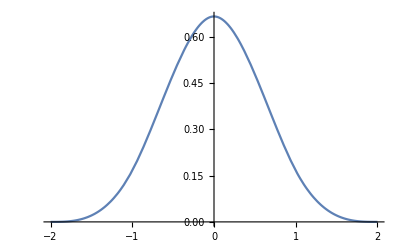

```mathematica
Plot[Convolve[UnitTriangle[x],UnitTriangle[x],x,y],{y,-2,2},PlotRange->Full]
```

(e)

```mathematica
Convolve[erf[x],boxcar[x],x,y]
```

1/2 (-ⅇ^(-1/2 (-1+y)^2) √(2/π)+ⅇ^(-y^2/2) √(2/π)-Convolve[1,UnitStep[-1+x],x,y]+Convolve[1,UnitStep[x],x,y]-(-1+y) Erf[(-1+y)/(√2)]+y Erf[y/(√2)])

```mathematica
Plot[1/2 (-ⅇ^(-1/2 (-1+y)^2) √(2/π)+ⅇ^(-y^2/2) √(2/π)-Convolve[1,UnitStep[-1+x],x,y]+Convolve[1,UnitStep[x],x,y]-(-1+y) Erf[(-1+y)/(√2)]+y Erf[y/(√2)]),{y,-3,5},PlotRange->Full]
```

-Graphics-

(f)

```mathematica
Plot[Convolve[nerf[x],estep[x],x,y],{y,-3,5},PlotRange->Automatic]
```

$Aborted

(g)

```mathematica
Plot[Convolve[estep[x],Convolve[tri[z],tri[z],z,x],x,y],{y,-3,5},PlotRange->Full]
```

(h)

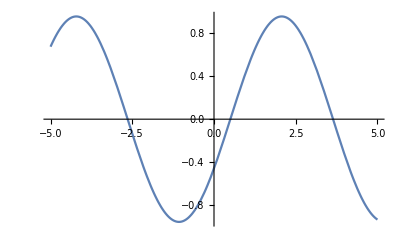

```mathematica
Plot[Convolve[Sin[x],boxcar[x],x,y],{y,-5,5},PlotRange->Full]
```

(i)

```mathematica
Plot[Convolve[Sin[x],gaussian[x],x,y],{y,-5,5},PlotRange->Full]
```

$Aborted

(j)

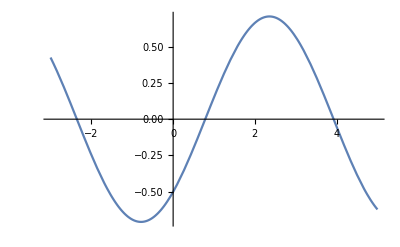

```mathematica
Plot[Convolve[Sin[x],estep[x],x,y],{y,-3,5},PlotRange->Full]
```

(k)

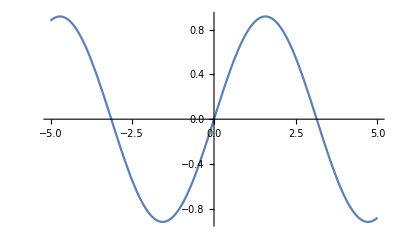

```mathematica
Plot[Convolve[Sin[x],tri[x],x,y],{y,-5,5},PlotRange->Full]
```

(l)

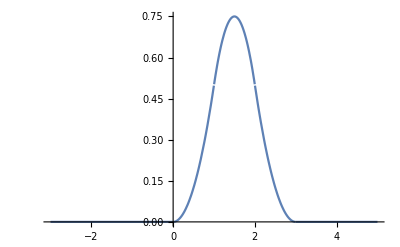

```mathematica
Plot[Convolve[boxcar[x],Convolve[boxcar[z],boxcar[z],z,x],x,y],{y,-3,5},PlotRange->Full]
```

(m)

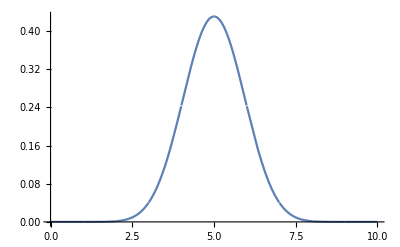

```mathematica
res=Nest[Convolve[#,boxcar[x],x,y]/.y->x&,boxcar[x],9];
p1=Plot[res,{x,0,10},PlotRange->All, PlotLegends->Automatic]
```

(n)

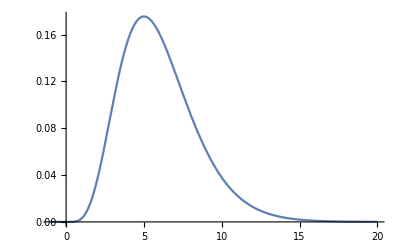

```mathematica
resE=Nest[Convolve[#,estep[x],x,y]/.y->x&,estep[x],5];
p1=Plot[resE,{x,-1,20},PlotRange->All, PlotLegends->Automatic]
```

(o)

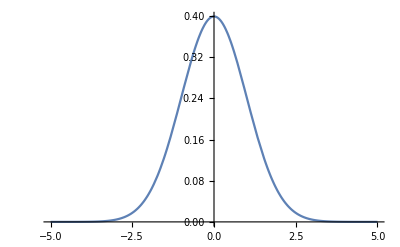

```mathematica
Plot[gaussian[x],{x,-5,5},PlotRange->Full]
```

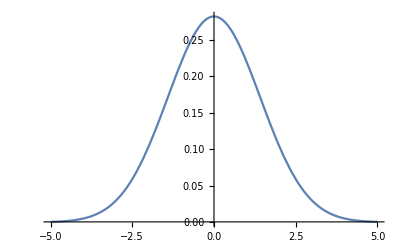

```mathematica
Plot[Convolve[gaussian[x],gaussian[x],x,y],{y,-5,5},PlotRange->Full]
```

```mathematica
FullSimplify[∑_(k=0)^∞ α^k]
```

1/(1-α)

```mathematica
FullSimplify[(1-α^(n+1))/(1-α)]
```

(-1+α^(1+n))/(-1+α)

```mathematica
Equivalent[(1-α^(n+1))/(1-α),(1+n)α^n]
```

(1+n) α^n⧦(1-α^(1+n))/(1-α)

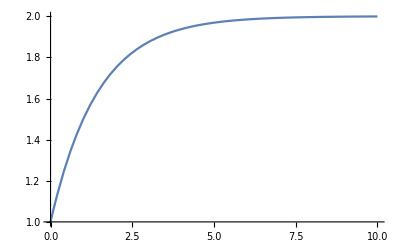

```mathematica
Plot[(-1+(.5)^(1+n))/(-1+.5),{n,0,10},PlotRange->Full]
```

### 6(2)

```mathematica
FullSimplify[(∫_(-∞)^∞ boxcar[x-y]*Exp[I*ω*y]ⅆy)/Exp[I*ω*x]]
```

(ⅈ (-1+Cos[ω])+Sin[ω])/ω

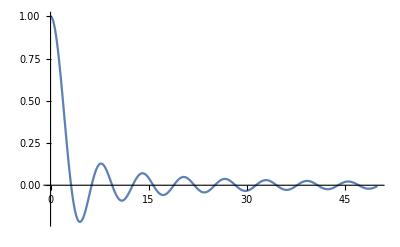

```mathematica
Plot[Re[(ⅈ (-1+Cos[ω])+Sin[ω])/ω],{ω,0,50},PlotRange->Full]
```

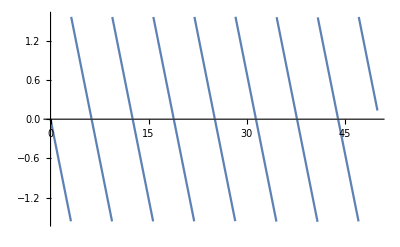

```mathematica
Plot[ArcTan[Im[(ⅈ (-1+Cos[ω])+Sin[ω])/ω]/Re[(ⅈ (-1+Cos[ω])+Sin[ω])/ω]],{ω,0,50},PlotRange->{-Pi/2,Pi/2}]
```

#### (b)

```mathematica
FullSimplify[(∫_(-∞)^∞ tri[x-y]*Exp[I*ω*y]ⅆy)/Exp[I*ω*x]]
```

(2-2 Cos[ω])/ω^2

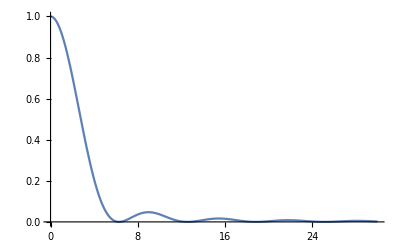

```mathematica
Plot[Re[(2-2 Cos[ω])/ω^2],{ω,0,30},PlotRange->Full]
```

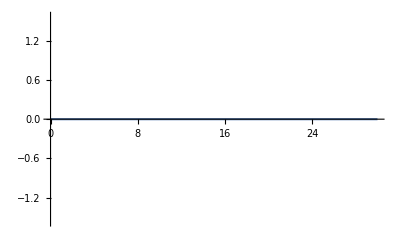

```mathematica
Plot[ArcTan[Im[(2-2 Cos[ω])/ω^2]/Re[(2-2 Cos[ω])/ω^2]],{ω,0,30},PlotRange->{-Pi/2,Pi/2}]
```

#### (c)

```mathematica
FullSimplify[(∫_(-∞)^∞ gaussian[x-y]*Exp[I*ω*y]ⅆy)/Exp[I*ω*x]]
```

1. ⅇ^(-ω^2/2)

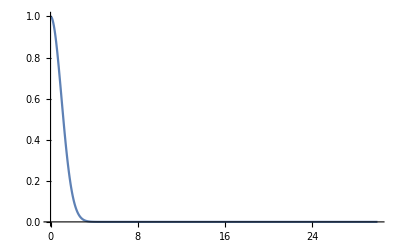

```mathematica
Plot[Re[ⅇ^(-ω^2/2)],{ω,0,30},PlotRange->Full]
```

```mathematica
Plot[ArcTan[Im[ⅇ^(-ω^2/2)]/Re[ⅇ^(-ω^2/2)]],{ω,0,30},PlotRange->{-Pi/2,Pi/2}]
```

-Graphics-

#### (d)

```mathematica
FullSimplify[(∫_(-∞)^∞ estep[x-y]*Exp[I*ω*y]ⅆy)/Exp[I*ω*x]]
```

-ⅈ/(-ⅈ+ω)

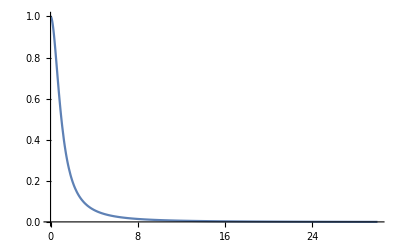

```mathematica
Plot[Re[-ⅈ/(-ⅈ+ω)],{ω,0,30},PlotRange->Full]
```

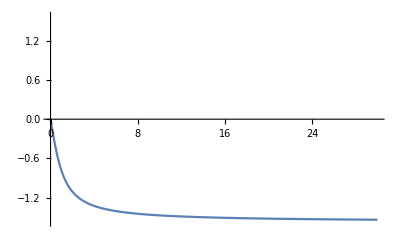

```mathematica
Plot[ArcTan[Im[-ⅈ/(-ⅈ+ω)]/Re[-ⅈ/(-ⅈ+ω)]],{ω,0,30},PlotRange->{-Pi/2,Pi/2}]
```

#### (e) I don’t know how to do it yet

```mathematica
estep2 = Convolve[estep[y],estep[y],y,x]
```

ⅇ^-x x UnitStep[x]

```mathematica
FourierTransform[ⅇ^-x x UnitStep[x],x,ω]
```

-1/(√(2 π) (ⅈ+ω)^2)

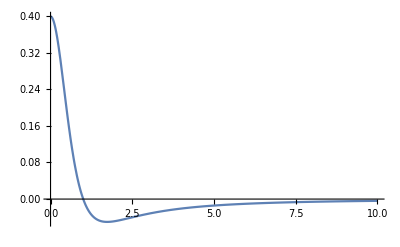

```mathematica
Plot[Re[-1/(√(2 π) (ⅈ+ω)^2)],{ω,0,10},PlotRange->Full]
```

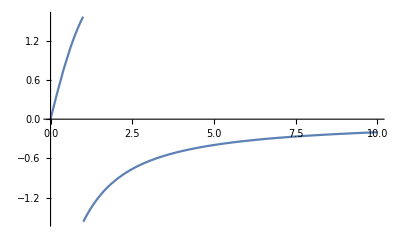

```mathematica
Plot[ArcTan[Im[-1/(√(2 π) (ⅈ+ω)^2)]/Re[-1/(√(2 π) (ⅈ+ω)^2)]],{ω,0,10},PlotRange->{-Pi/2,Pi/2}]
```

#### (f)

```mathematica
f6=FullSimplify[FourierTransform[poisson[θ,r],r,ω]]
```

-√(2 π) DiracDelta[ω]+√(2 π) (-ⅈ Cos[ω Cos[θ]]+Sin[ω Cos[θ]]) (Cos[θ+ⅈ ω Sin[θ]] ((Piecewise[{{-HeavisideTheta[-ω], Im[Cos[θ]]<Re[Sin[θ]]}, {HeavisideTheta[ω], True}}])+HeavisideTheta[ω Sign[Im[Cos[θ]]+Re[Sin[θ]]]] Sign[Im[Cos[θ]]+Re[Sin[θ]]])+ⅈ ((Piecewise[{{HeavisideTheta[-ω], Im[Cos[θ]]<Re[Sin[θ]]}, {-HeavisideTheta[ω], True}}])+HeavisideTheta[ω Sign[Im[Cos[θ]]+Re[Sin[θ]]]] Sign[Im[Cos[θ]]+Re[Sin[θ]]]) Sin[θ+ⅈ ω Sin[θ]])

```mathematica
Manipulate[Plot[Re[-√(2 π) DiracDelta[ω]+√(2 π) (-ⅈ Cos[ω Cos[θ]]+Sin[ω Cos[θ]]) (Cos[θ+ⅈ ω Sin[θ]] ((Piecewise[{{-HeavisideTheta[-ω], Im[Cos[θ]]<Re[Sin[θ]]}, {HeavisideTheta[ω], True}}])+HeavisideTheta[ω Sign[Im[Cos[θ]]+Re[Sin[θ]]]] Sign[Im[Cos[θ]]+Re[Sin[θ]]])+ⅈ ((Piecewise[{{HeavisideTheta[-ω], Im[Cos[θ]]<Re[Sin[θ]]}, {-HeavisideTheta[ω], True}}])+HeavisideTheta[ω Sign[Im[Cos[θ]]+Re[Sin[θ]]]] Sign[Im[Cos[θ]]+Re[Sin[θ]]]) Sin[θ+ⅈ ω Sin[θ]])],{ω,0,10},PlotRange->{-3,3}],{θ,0,2Pi}]
```

```mathematica
Manipulate[Plot[ArcTan[Im[-√(2 π) DiracDelta[ω]+√(2 π) (-ⅈ Cos[ω Cos[θ]]+Sin[ω Cos[θ]]) (Cos[θ+ⅈ ω Sin[θ]] ((Piecewise[{{-HeavisideTheta[-ω], Im[Cos[θ]]<Re[Sin[θ]]}, {HeavisideTheta[ω], True}}])+HeavisideTheta[ω Sign[Im[Cos[θ]]+Re[Sin[θ]]]] Sign[Im[Cos[θ]]+Re[Sin[θ]]])+ⅈ ((Piecewise[{{HeavisideTheta[-ω], Im[Cos[θ]]<Re[Sin[θ]]}, {-HeavisideTheta[ω], True}}])+HeavisideTheta[ω Sign[Im[Cos[θ]]+Re[Sin[θ]]]] Sign[Im[Cos[θ]]+Re[Sin[θ]]]) Sin[θ+ⅈ ω Sin[θ]])]/Re[-√(2 π) DiracDelta[ω]+√(2 π) (-ⅈ Cos[ω Cos[θ]]+Sin[ω Cos[θ]]) (Cos[θ+ⅈ ω Sin[θ]] ((Piecewise[{{-HeavisideTheta[-ω], Im[Cos[θ]]<Re[Sin[θ]]}, {HeavisideTheta[ω], True}}])+HeavisideTheta[ω Sign[Im[Cos[θ]]+Re[Sin[θ]]]] Sign[Im[Cos[θ]]+Re[Sin[θ]]])+ⅈ ((Piecewise[{{HeavisideTheta[-ω], Im[Cos[θ]]<Re[Sin[θ]]}, {-HeavisideTheta[ω], True}}])+HeavisideTheta[ω Sign[Im[Cos[θ]]+Re[Sin[θ]]]] Sign[Im[Cos[θ]]+Re[Sin[θ]]]) Sin[θ+ⅈ ω Sin[θ]])]],{ω,0,30},PlotRange->{-Pi/2,Pi/2}],{θ,0,2Pi}]
```

#### (g)

```mathematica
FullSimplify[FourierTransform[dirichlet[n,x],x,ω]]
```

Csc[0.5 n] ((0.+0. ⅈ)+(0.+1.25331 ⅈ) ⅇ^((0.-0.5 ⅈ) n) DiracDelta[-n+ω])

```mathematica
Manipulate[Plot[Re[Csc[0.5 n] ((0.+0. ⅈ)+(0.+1.2533141373155001 ⅈ) ⅇ^((0.-0.5 ⅈ) n) DiracDelta[-n+ω])],{ω,0,10},PerformanceGoal->"Quality"],{n,1,100}]
```

### 7 Heat Kernel

```mathematica
h[t_,x_]:=(t^(-1/2))*gaussian[x*t^(-1/2)];
```

#### (a)

```mathematica
FullSimplify[∫_(x-1)^x h[t,y]ⅆy]
```

(0.5 (-((-1+x) Erf[(√((-1+x)^2/t^1.))/(√2)])/(√((-1+x)^2/t^1.))+(x Erf[(√(x^2/t^1.))/(√2)])/(√(x^2/t^1.))))/t^0.5

#### (b)

```mathematica
FullSimplify[∫_(-∞)^∞ h[t,y]Sin[5*(x-y)]ⅆy]
```

ConditionalExpression[1. ⅇ^(-(25 t^1.)/2) Sin[5 x],Re[t^1.]>0]

#### (c)

```mathematica
FullSimplify[∫_(x-1)^x h[t,y]Sin[5*(x-y)]ⅆy]
```

ⅇ^(-12.5 t^1.-(0.+5. ⅈ) x) (-0.25 Erfi[3.53553 t^0.5+((0.+0.707107 ⅈ) (-1.+x))/t^0.5]+ⅇ^((0.+10. ⅈ) x) ((0.-0.25 ⅈ) Erf[(0.707107-(0.+3.53553 ⅈ) t^1.-0.707107 x)/t^0.5]+0.25 Erfi[3.53553 t^0.5-((0.+0.707107 ⅈ) x)/t^0.5])+0.25 Erfi[3.53553 t^0.5+((0.+0.707107 ⅈ) x)/t^0.5])

#### (d)

```mathematica
FullSimplify[∫_(-∞)^∞ h[t,y]estep[x-y]ⅆy]
```

ConditionalExpression[(ⅇ^(t^1./2-x) (0.5 t^0.5 √(t^1.-2. x+x^2/t^1.)+(-0.5 t^1.+0.5 x) Erf[(√(((t^1.-x)^2)/t^1.))/(√2)]))/(t^0.5 √(((t^1.-x)^2)/t^1.)),Re[t^1.]≥0]

#### (e)

```mathematica
tri75[x_]:=Piecewise[{{tri[x-1],x≥0},{-1*tri[x+1],x<0}}]
```

```mathematica
FullSimplify[∫_(-∞)^∞ h[t,y]tri75[x-y]ⅆy]
```

(-0.797885 ⅇ^(-(0.5 (1.-1. x)^2)/t)+0.398942 ⅇ^(-(0.5 (2.-1. x)^2)/t)+0.797885 ⅇ^(-(0.5 (1.+1. x)^2)/t)-0.398942 ⅇ^(-(0.5 (2.+1. x)^2)/t)) √t+(-1.+0.5 x) Erf[(0.707107 (-2.+x))/(√t)]+(1.-1. x) Erf[(0.707107 (-1.+x))/(√t)]+(1.+1. x) Erf[(0.707107 (1.+x))/(√t)]-1. Erf[(0.707107 (2.+x))/(√t)]-0.5 x Erf[(0.707107 (2.+x))/(√t)]

### 8. Visualizing solution to the heat equation on the line

```mathematica
u71[t_,x_]=(0.5 (-((-1+x) Erf[(√((-1+x)^2/t^1.))/(√2)])/(√((-1+x)^2/t^1.))+(x Erf[(√(x^2/t^1.))/(√2)])/(√(x^2/t^1.))))/t^0.5;
```

```mathematica
FullSimplify[(0.5 (-((-1+x) Erf[(√((-1+x)^2/t^1.))/(√2)])/(√((-1+x)^2/t^1.))+(x Erf[(√(x^2/t^1.))/(√2)])/(√(x^2/t^1.))))/t^0.5]
```

(0.5 (-((-1+x) Erf[(√((-1+x)^2/t^1.))/(√2)])/(√((-1+x)^2/t^1.))+(x Erf[(√(x^2/t^1.))/(√2)])/(√(x^2/t^1.))))/t^0.5

```mathematica
Manipulate[Plot[u71[t,x],{x,-5,5},PlotRange->{0,1.2}],{t,0.001,5}]
```

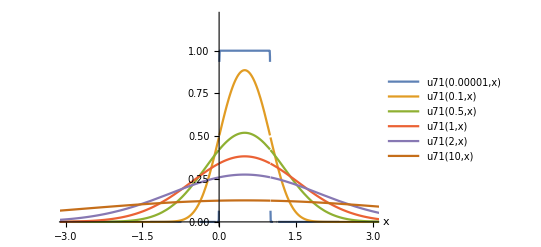

```mathematica
Plot[{u71[0.00001,x],u71[0.1,x],u71[.5,x],u71[1,x],u71[2,x],u71[10,x]},{x,-5,10},PlotRange->{{-3,3},{0,1.2}},PlotLegends->"Expressions",AxesLabel->Automatic]
```

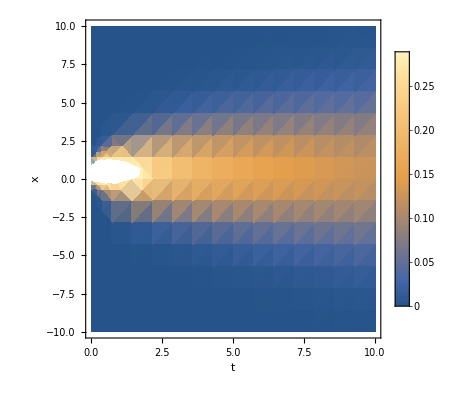

```mathematica
DensityPlot[u71[t,x],{t,0,10},{x,-10,10},PlotLegends->Automatic,FrameLabel->Automatic]
```

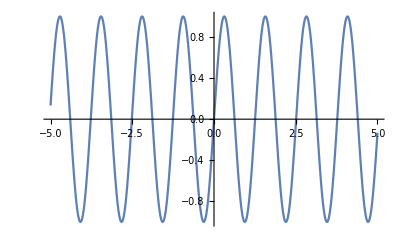

```mathematica
u72[t_,x_]:=1. ⅇ^(-(25 t^1.)/2) Sin[5 x];
Plot[u72[0.000001,x],{x,-5,5}]
```

```mathematica
Manipulate[Plot[u72[t,x],{x,-5,5},PlotRange->{-1,1}],{t,0.000,.5}]
```

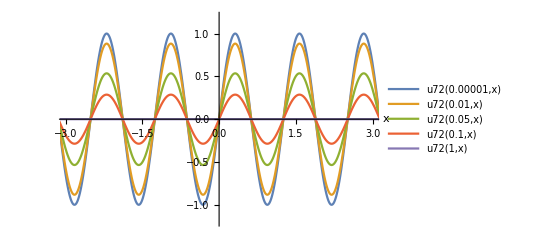

```mathematica
Plot[{u72[0.00001,x],u72[0.01,x],u72[.05,x],u72[.1,x],u72[1,x]},{x,-5,10},PlotRange->{{-3,3},{-1.2,1.2}},PlotLegends->"Expressions",AxesLabel->Automatic]
```

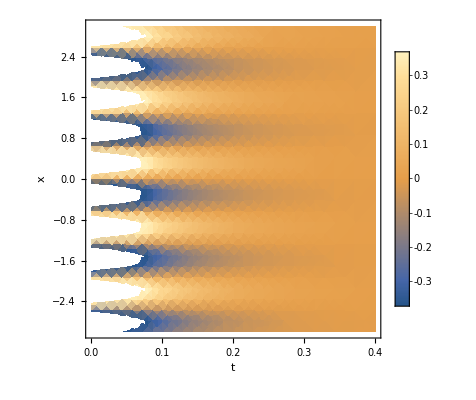

```mathematica
DensityPlot[u72[t,x],{t,0,.4},{x,-3,3},PlotLegends->Automatic,PerformanceGoal->"Quality",FrameLabel->Automatic]
```

```mathematica
u73[t_,x_]=ⅇ^(-12.5 t^1.-(0.+5. ⅈ) x) (-0.25 Erfi[3.5355339059327373 t^0.5+((0.+0.7071067811865475 ⅈ) (-1.`15.954589770191003+x))/t^0.5]+ⅇ^((0.+10. ⅈ) x) ((0.-0.25 ⅈ) Erf[(0.7071067811865475-(0.+3.5355339059327373 ⅈ) t^1.-0.7071067811865475 x)/t^0.5]+0.25 Erfi[3.5355339059327373 t^0.5-((0.+0.7071067811865475 ⅈ) x)/t^0.5])+0.25 Erfi[3.5355339059327373 t^0.5+((0.+0.7071067811865475 ⅈ) x)/t^0.5]);
```

```mathematica
Manipulate[Plot[u73[t,x],{x,-5,5},PlotRange->{{-2,2},{-1,1}}],{t,0.0001,5}]
```

General::munfl: Exp[-179994.-29.9991 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-179994.+29.9991 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-124996.+24.9991 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

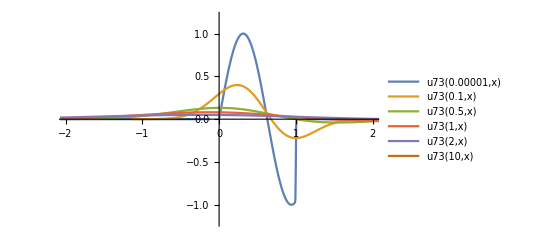

```mathematica
Plot[{u73[0.00001,x],u73[0.1,x],u73[.5,x],u73[1,x],u73[2,x],u73[10,x]},{x,-5,10},PlotRange->{{-2,2},{-1.2,1.2}},PlotLegends->"Expressions"]
```

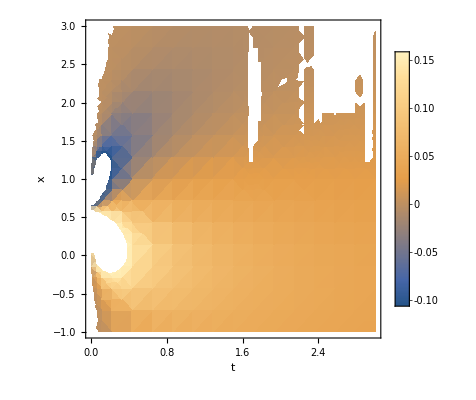

```mathematica
DensityPlot[u73[t,x],{t,0,3},{x,-1,3},PerformanceGoal->"Quality",PlotLegends->Automatic,FrameLabel->Automatic]
```

```mathematica
u74[t_,x_]:=(ⅇ^(t^1./2-x) (0.5000000000000001 t^0.5 √(t^1.-2. x+x^2/t^1.)+(-0.5 t^1.+0.5 x) Erf[(√(((t^1.-x)^2)/t^1.))/(√2)]))/(t^0.5 √(((t^1.-x)^2)/t^1.));
```

```mathematica
Manipulate[Plot[u74[t,x],{x,-5,10},PlotRange->{{-5,10},{-.5,2}}],{t,0.0001,10}]
```

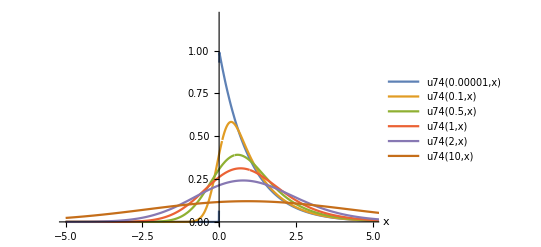

```mathematica
Plot[{u74[0.00001,x],u74[0.1,x],u74[.5,x],u74[1,x],u74[2,x],u74[10,x]},{x,-5,10},PlotRange->{{-5,5},{0,1.2}},PlotLegends->"Expressions",AxesLabel->Automatic]
```

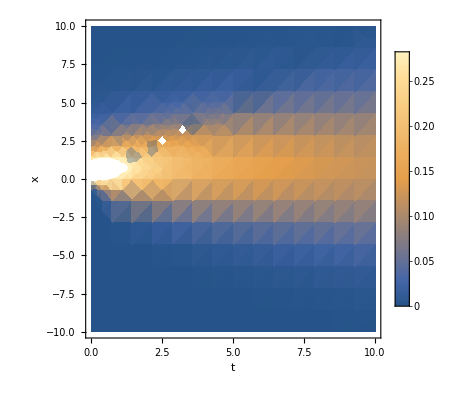

```mathematica
DensityPlot[u74[t,x],{t,0,10},{x,-10,10},PerformanceGoal->"Quality",PlotLegends->Automatic,FrameLabel->Automatic]
```

```mathematica
u75a[t_,x_]:=(-0.7978845608028655 ⅇ^(-(0.5000000000000001 (1.-1. x)^2)/t)+0.39894228040143276 ⅇ^(-(0.5000000000000001 (2.-1. x)^2)/t)+0.7978845608028655 ⅇ^(-(0.5000000000000001 (1.+1. x)^2)/t)-0.39894228040143276 ⅇ^(-(0.5000000000000001 (2.+1. x)^2)/t)) √t+(-1.0000000000000002+0.5000000000000001 x) Erf[(0.7071067811865476 (-2.+x))/(√t)]+(1.0000000000000002-1.0000000000000002 x) Erf[(0.7071067811865476 (-1.+x))/(√t)]+(1.0000000000000002+1.0000000000000002 x) Erf[(0.7071067811865476 (1.+x))/(√t)]-1.0000000000000002 Erf[(0.7071067811865476 (2.+x))/(√t)]-0.5000000000000001 x Erf[(0.7071067811865476 (2.+x))/(√t)];
```

```mathematica
Manipulate[Plot[u75a[t,x],{x,-5,10},PlotRange->{{-5,5},{-1.2,1.2}}],{t,0.00001,10}]
```

General::munfl: Exp[-1.79982×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.44979×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-799877.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

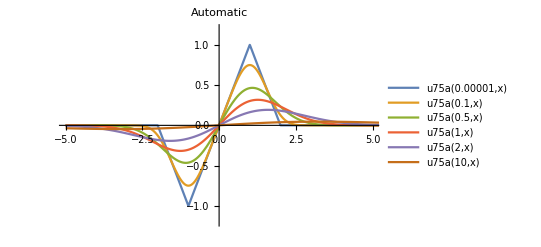

```mathematica
Plot[{u75a[0.00001,x],u75a[0.1,x],u75a[.5,x],u75a[1,x],u75a[2,x],u75a[10,x]},{x,-5,10},PlotRange->{{-5,5},{-1.2,1.2}},PlotLegends->"Expressions",PlotLabel->Automatic]
```

General::munfl: Exp[-8467.8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-10077.6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5668.2] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

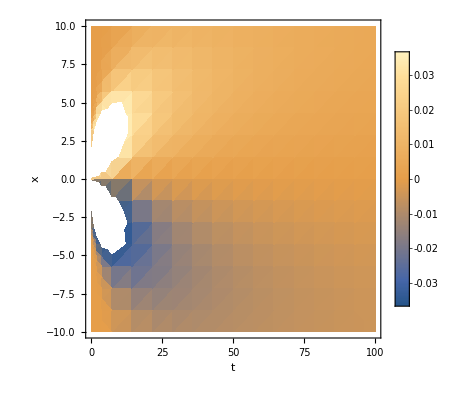

```mathematica
DensityPlot[u75a[t,x],{t,0,100},{x,-10,10},PlotLegends->Automatic,FrameLabel->Automatic]
```

```mathematica
FullSimplify[Convolve[h[t,y],boxcar[y],y,x]]
```

1/2 (-Erf[(-1+x)/(√2 √t)]+Erf[x/(√2 √t)])

```mathematica
∫_(x-1)^x h[t,y]ⅆy
```

1/2 (-Erf[(-1+x)/(√2 √t)]+Erf[x/(√2 √t)])

```mathematica
a1[n_,x_]:=(n/Sqrt[(n/2+x)(n/2-x)])^n
```

```mathematica
Plot[Ω1[1000,x],{x,0,100}, PlotRange->Full]
```

-Graphics-

```mathematica
Ω[n_,x_]:=(2/Sqrt[1-(4x^2)/n^2])^n((1-(2x)/n)/(1+(2x)/n))^x
```

```mathematica
Ω1[n_,x_]:=2^n*Exp[(-4x^2)/n]
```

```mathematica
Series[(1+(2x)/n)/(1-(2x)/n),{x,0,5}]
```

1+(4 x)/n+(8 x^2)/n^2+(16 x^3)/n^3+(32 x^4)/n^4+(64 x^5)/n^5+O[x]^6

```mathematica
Series[Exp[x],{x,0,5}]
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120+O[x]^6

```mathematica
FullSimplify[(1+(2x)/n)/(1-(2x)/n)]
```

(n+2 x)/(n-2 x)

```mathematica
Series[Sqrt[(1-(4x^2)/n)^n],{x,0,5}]
```

1-2 x^2+(2-4/n) x^4+O[x]^6

```mathematica
Solve[e==Sqrt[(1-(4x^2)/n)^n]*((1+(2x)/n)/(1-(2x)/n))^x,x]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[e==((1+(2 x)/n)/(1-(2 x)/n))^x √((1-(4 x^2)/n)^n),x]

```mathematica
Ser
```